```mathematica
(*
ScaledDirectory is the location of the scaled files. FinalDirectory is where your files will be saved. 
You will have to change these to your directories.
You will have to create the final directory folder for the output files.
*)
voltage =250;
DataDirectory=StringJoin["C:\\Users\\maruk\\Desktop\\Research\\PHY242\\retake\\Europium J=7-2\\2022-06-14 Voltage\\",ToString[voltage]];
SetDirectory[DataDirectory];
SaveDirectory ="C:\\Users\\maruk\\Desktop\\Research\\PHY242\\retake\\Europium J=7-2\\2022-06-14 Voltage\\fit_result";
fnup=FileNames["scanup*"]
fndown=FileNames["scandown*"]
```

{scanup01.txt,scanup02.txt,scanup03.txt,scanup04.txt}

{scandown01.txt,scandown02.txt,scandown03.txt,scandown04.txt}

```mathematica
Clear[AES,BES,Ae153,Be153];
Clear[aArray,f0,gArray];
L[f_]=aArray/(1+4 (f-f0)^2/gArray^2);
transitions=Join[Transpose[sorted151],Transpose[sorted153]];
transitions = Select[transitions,Abs[#[[3]]]<4&];
```

```mathematica
f0=transitions[[All,4]];
aArrayguess=Table[{ToExpression["a"<>If[i<10,"0"<>ToString[i],ToString[i]]],If[i≤Floor[Length[transitions]/2],0.1,0.02]},{i,1,Length[f0]}];
aArray=aArrayguess[[All,1]];
gArrayguess = Table[{ToExpression["γ"<>If[i<10,"0"<>ToString[i],ToString[i]]],20},{i,1,Length[f0]}];
gArray=gArrayguess[[All,1]];
Clear[AGS,BGS,AES,BES,Ae153,Be153];
AGS=-20.0523;BGS=-0.7012;
Ag=AGS;
Bg =BGS;
Ae=AES;
Be=BES;
Ag153 =Ag153m;
Bg153 =Bg153m;
(*AES=Ae9Halvesm;
BES=Be9Halvesm;
Ae153=Ae153m;
Be153=Be153m;*)
tofit[f_]=Tr[L[f]]+off+m (f-fcog);
var=Join[aArrayguess,gArrayguess,{{fcog,4090.0},{off,0.01},{m,0},{nu,-2977},{Ae153,Ae153m},{Be153,Be153m},{AES,Ae9Halvesm},{BES,Be9Halvesm}}];
```

```mathematica
fit[in_,print_]:=Module[{},
nlm=NonlinearModelFit[data,tofit[f],var,f];
p1=ListLinePlot[data,Frame->True,FrameStyle->Directive[Black,18],PlotStyle->{Black},AspectRatio->1/5,ImageSize->800,FrameLabel->{"f (MHz)","Signal (arb units)"},PlotRange->All];
p2=Plot[Evaluate[Normal[nlm]],{f,data[[1,1]],data[[-1,1]]},PlotStyle->Red,PlotRange->All];
res=ListLinePlot[Transpose[{data[[All,1]],Evaluate[nlm["FitResiduals"]]}],Frame->True,FrameStyle->Black,PlotStyle->Black,AspectRatio->1/5,ImageSize->800,FrameLabel->{"f (MHz)","Residuals (arb units)"},PlotRange->All];
Print[Show[p1,p2]];
Print[res];
Print[Around[fcog/.nlm["BestFitParameters"],2 nlm["ParameterErrors"][[2*Length[f0]+1]]]];
];
```

```mathematica
fit2[in_]:=Module[{out},
nlm=NonlinearModelFit[data,tofit[f],var,f];
fitResult = nlm["BestFitParameters"];
errors = nlm["ParameterErrors"];fitResult;
gammas =gArray/.fitResult;
Ae151result = Around[AES/.fitResult,2 errors[[-2]]];
Be151result=Around[BES/.fitResult,2errors[[-1]]];
Be153Result=Around[Be153/.fitResult,2errors[[-3]]];
Ae153Result=Around[Ae153/.fitResult,2errors[[-4]]];
out ={Around[fcog/.fitResult,2errors[[-8]]],Median[gammas],Around[nu/.fitResult,2errors[[-5]]],Ae151result,Be151result,Be153Result,Ae153Result};
out
];
```

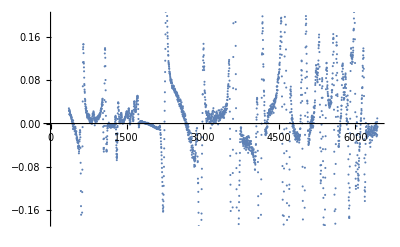

```mathematica
data=Drop[Import["scanup01.txt","Table"][[All,{1,3}]],150];
ListPlot[data]
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

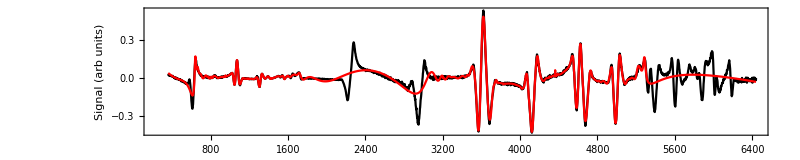

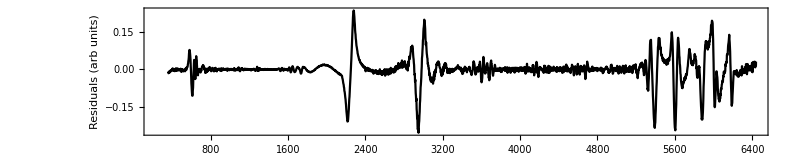

4087.5.

```mathematica
fit[data,"Y"]
```

```mathematica
nlm["RSquared"]
nlm["ParameterTable"]
```

NonlinearModelFit[{{361.782,0.027973},{364.212,0.023173},{366.652,0.024385},{368.892,0.024224},2590,{6433.57,-0.0210407},{6435.86,0.00948328},{6438.12,-0.00524272},{6439.61,-0.00663172}},2,f][RSquared]
 |  |  |  |

NonlinearModelFit[{{361.782,0.027973},{364.212,0.023173},{366.652,0.024385},{368.892,0.024224},2590,{6433.57,-0.0210407},{6435.86,0.00948328},{6438.12,-0.00524272},{6439.61,-0.00663172}},2,f][ParameterTable]
 |  |  |  |

-Graphics-

```mathematica
aArrayVal=aArray/.nlm["BestFitParameters"];
aArrayguess2 = Transpose[{aArray,aArrayVal}];
```

ReplaceAll::reps: {NonlinearModelFit[{{361.782,0.027973},{364.212,0.023173},{366.652,0.024385},{368.892,0.024224},{371.064,0.017113},{373.419,0.016771},{375.913,0.02473},{378.356,0.022192},{380.863,0.021313},{383.146,0.01981},«2588»},«1»,Join[«1»],f][…s]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Transpose::nmtx: The first two levels of {{a01,a02,a03,a04,a05,a06,a07,a08,a09,a10,«144»},{a01,a02,a03,a04,a05,a06,a07,a08,a09,a10,«144»}/.«1»[BestFitParameters]} cannot be transposed.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {{a01,a02,a03,a04,a05,a06,a07,a08,a09,a10,«144»},{a01,a02,a03,a04,a05,a06,a07,a08,a09,a10,«144»}/.«1»[BestFitParameters]}.

```mathematica
fcogup={};
gammaup={};
nuup={};
AESup={};
BESup={};
Ae153up={};
Be153up={};
(*var=Join[aArrayguess2,gArrayguess,{{fcog,4111.0},{off,0.01},{m,0},{nu,-2977},{Ae153,Ae153m},{Be153,Be153m},{AES,Ae9Halvesm},{BES,Be9Halvesm}}];*)
For[i=1,i<=Length[fnup],
data=Drop[Import[fnup[[i]],"Table"][[All,{1,3}]],150];
fitup =fit2[data];
AppendTo[fcogup,fitup[[1]]];
AppendTo[gammaup,fitup[[2]]];
AppendTo[nuup,fitup[[3]]];
AppendTo[AESup,fitup[[4]]];
AppendTo[BESup,fitup[[5]]];
AppendTo[Ae153up,fitup[[6]]];
AppendTo[Be153up,fitup[[7]]];
Print[i,"complete"];
i++];
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {{a01,a02,a03,a04,a05,a06,a07,a08,a09,a10,«144»},{a01,a02,a03,a04,a05,a06,a07,a08,a09,a10,«144»}/.«1»[BestFitParameters]}.

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

ReplaceAll::reps: {fitResult} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification errors⟦-2⟧ is longer than depth of object.

ReplaceAll::reps: {fitResult} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification errors⟦-1⟧ is longer than depth of object.

Part::partd: Part specification errors⟦-3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

1complete

2complete

3complete

4complete

```mathematica
fcogdown={};
gammadown={};
nudown={};
AESdown={};
BESdown={};
Ae153down={};
Be153down={};
(*var=Join[aArrayguess2,gArrayguess,{{fcog,4110.0},{off,0.01},{m,0},{nu,-2977},{Ae153,Ae153m},{Be153,Be153m},{AES,Ae9Halvesm},{BES,Be9Halvesm}}];*)
For[i=1,i<=Length[fndown],
data=Drop[Import[fndown[[i]],"Table"][[All,{1,3}]],150];
(*If[EvenQ[i],fcogGuess=3625,3627];*)
fitdown =fit2[data];
AppendTo[fcogdown,fitdown[[1]]];
AppendTo[gammadown,fitdown[[2]]];
AppendTo[nudown,fitdown[[3]]];
AppendTo[AESdown,fitdown[[4]]];
AppendTo[BESdown,fitdown[[5]]];
AppendTo[Ae153down,fitdown[[6]]];
AppendTo[Be153down,fitdown[[7]]];
Print[i,"complete"];
i++];
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {{a01,a02,a03,a04,a05,a06,a07,a08,a09,a10,«144»},{a01,a02,a03,a04,a05,a06,a07,a08,a09,a10,«144»}/.«1»[BestFitParameters]}.

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

ReplaceAll::reps: {fitResult} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

1complete

ReplaceAll::reps: {fitResult} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

2complete

ReplaceAll::reps: {fitResult} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

3complete

4complete

```mathematica
ListPlot[{fcogup,fcogdown},PlotRange->All]
ListPlot[{Ae153up,Ae153down},PlotRange->All]
ListPlot[{gammaup,gammadown},PlotRange->All]
ListPlot[{nuup,nudown},PlotRange->All]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
fcogResult =Join[fcogup[[All,1]],fcogdown[[All,1]]];
gammaResult =Join[gammaup,gammadown];
nuResult = Join[nuup[[All,1]],nudown[[All,1]]];
AESResult =Join[AESup[[All,1]],AESdown[[All,1]]];
BESResult =Join[BESup[[All,1]],BESdown[[All,1]]];
Ae153fit = Join[Ae153up[[All,1]],Ae153down[[All,1]]];
Be153fit= Join[Be153up[[All,1]],Be153down[[All,1]]];

fcogError =Mean[Join[fcogup[[All,2]],fcogdown[[All,2]]]];
nuError =Mean[Join[nuup[[All,2]],nudown[[All,2]]]];
AESError =Max[{Mean[Join[AESup[[All,2]],AESdown[[All,2]]]],StandardDeviation[AESResult]}];
BESError =Max[{Mean[Join[BESup[[All,2]],BESdown[[All,2]]]],StandardDeviation[BESResult]}];
Ae153Error =Mean[Join[Ae153up[[All,2]],Ae153down[[All,2]]]];
Be153Error =Mean[Join[Be153up[[All,2]],Be153down[[All,2]]]];
```

```mathematica
voltageError =0;
resultTable=Transpose[Join[{Join[{"","Mean value","error"},Table["",{n,1,Length[fcogResult]}]]},{Flatten[{"Pressure",voltage,voltageError,Table[voltage,{n,1,Length[fcogResult]}]}],
Flatten[{"fcog",Mean[fcogResult],fcogError,fcogResult}],
Flatten[{"gamma",Mean[gammaResult],"",gammaResult}],
Flatten[{"isotope shift",Mean[nuResult],nuError,nuResult}],
Flatten[{"AES",Mean[AESResult],AESError,AESResult}],
Flatten[{"BES",Mean[BESResult],BESError,BESResult}],
Flatten[{"BE153",Mean[Ae153fit],Ae153Error,Ae153fit}],
Flatten[{"AE153",Mean[Be153fit],Be153Error,Be153fit}]}]];
resultTable//TableForm
```

| Pressure | fcog | gamma | isotope shift | AES | BES | BE153 | AE153
Mean value | 250 | fcog/.fitResult | Median[{γ01,γ02,γ03,γ04,γ05,γ06,γ07,γ08,γ09,γ10,γ11,γ12,γ13,γ14,γ15,γ16,γ17,γ18,γ19,γ20,γ21,γ22,γ23,γ24,γ25,γ26,γ27,γ28,γ29,γ30,γ31,γ32,γ33,γ34,γ35,γ36,γ37,γ38,γ39,γ40,γ41,γ42,γ43,γ44,γ45,γ46,γ47,γ48,γ49,γ50,γ51,γ52,γ53,γ54,γ55,γ56,γ57,γ58,γ59,γ60,γ61,γ62,γ63,γ64,γ65,γ66,γ67,γ68,γ69,γ70,γ71,γ72,γ73,γ74,γ75,γ76,γ77,γ78,γ79,γ80,γ81,γ82,γ83,γ84,γ85,γ86,γ87,γ88,γ89,γ90,γ91,γ92,γ93,γ94,γ95,γ96,γ97,γ98,γ99,γ100,γ101,γ102,γ103,γ104,γ105,γ106,γ107,γ108,γ109,γ110,γ111,γ112,γ113,γ114,γ115,γ116,γ117,γ118,γ119,γ120,γ121,γ122,γ123,γ124,γ125,γ126,γ127,γ128,γ129,γ130,γ131,γ132,γ133,γ134,γ135,γ136,γ137,γ138,γ139,γ140,γ141,γ142,γ143,γ144,γ145,γ146,γ147,γ148,γ149,γ150,γ151,γ152,γ153,γ154}/.fitResult] | nu/.fitResult | AES/.fitResult | BES/.fitResult | Be153/.fitResult | Ae153/.fitResult
error | 0 | 2 errors⟦-8⟧ |  | 2 errors⟦-5⟧ | Max[0,2 errors⟦-2⟧] | Max[0,2 errors⟦-1⟧] | 2 errors⟦-3⟧ | 2 errors⟦-4⟧
 | 250 | fcog/.fitResult | Median[{γ01,γ02,γ03,γ04,γ05,γ06,γ07,γ08,γ09,γ10,γ11,γ12,γ13,γ14,γ15,γ16,γ17,γ18,γ19,γ20,γ21,γ22,γ23,γ24,γ25,γ26,γ27,γ28,γ29,γ30,γ31,γ32,γ33,γ34,γ35,γ36,γ37,γ38,γ39,γ40,γ41,γ42,γ43,γ44,γ45,γ46,γ47,γ48,γ49,γ50,γ51,γ52,γ53,γ54,γ55,γ56,γ57,γ58,γ59,γ60,γ61,γ62,γ63,γ64,γ65,γ66,γ67,γ68,γ69,γ70,γ71,γ72,γ73,γ74,γ75,γ76,γ77,γ78,γ79,γ80,γ81,γ82,γ83,γ84,γ85,γ86,γ87,γ88,γ89,γ90,γ91,γ92,γ93,γ94,γ95,γ96,γ97,γ98,γ99,γ100,γ101,γ102,γ103,γ104,γ105,γ106,γ107,γ108,γ109,γ110,γ111,γ112,γ113,γ114,γ115,γ116,γ117,γ118,γ119,γ120,γ121,γ122,γ123,γ124,γ125,γ126,γ127,γ128,γ129,γ130,γ131,γ132,γ133,γ134,γ135,γ136,γ137,γ138,γ139,γ140,γ141,γ142,γ143,γ144,γ145,γ146,γ147,γ148,γ149,γ150,γ151,γ152,γ153,γ154}/.fitResult] | nu/.fitResult | AES/.fitResult | BES/.fitResult | Be153/.fitResult | Ae153/.fitResult
 | 250 | fcog/.fitResult | Median[{γ01,γ02,γ03,γ04,γ05,γ06,γ07,γ08,γ09,γ10,γ11,γ12,γ13,γ14,γ15,γ16,γ17,γ18,γ19,γ20,γ21,γ22,γ23,γ24,γ25,γ26,γ27,γ28,γ29,γ30,γ31,γ32,γ33,γ34,γ35,γ36,γ37,γ38,γ39,γ40,γ41,γ42,γ43,γ44,γ45,γ46,γ47,γ48,γ49,γ50,γ51,γ52,γ53,γ54,γ55,γ56,γ57,γ58,γ59,γ60,γ61,γ62,γ63,γ64,γ65,γ66,γ67,γ68,γ69,γ70,γ71,γ72,γ73,γ74,γ75,γ76,γ77,γ78,γ79,γ80,γ81,γ82,γ83,γ84,γ85,γ86,γ87,γ88,γ89,γ90,γ91,γ92,γ93,γ94,γ95,γ96,γ97,γ98,γ99,γ100,γ101,γ102,γ103,γ104,γ105,γ106,γ107,γ108,γ109,γ110,γ111,γ112,γ113,γ114,γ115,γ116,γ117,γ118,γ119,γ120,γ121,γ122,γ123,γ124,γ125,γ126,γ127,γ128,γ129,γ130,γ131,γ132,γ133,γ134,γ135,γ136,γ137,γ138,γ139,γ140,γ141,γ142,γ143,γ144,γ145,γ146,γ147,γ148,γ149,γ150,γ151,γ152,γ153,γ154}/.fitResult] | nu/.fitResult | AES/.fitResult | BES/.fitResult | Be153/.fitResult | Ae153/.fitResult
 | 250 | fcog/.fitResult | Median[{γ01,γ02,γ03,γ04,γ05,γ06,γ07,γ08,γ09,γ10,γ11,γ12,γ13,γ14,γ15,γ16,γ17,γ18,γ19,γ20,γ21,γ22,γ23,γ24,γ25,γ26,γ27,γ28,γ29,γ30,γ31,γ32,γ33,γ34,γ35,γ36,γ37,γ38,γ39,γ40,γ41,γ42,γ43,γ44,γ45,γ46,γ47,γ48,γ49,γ50,γ51,γ52,γ53,γ54,γ55,γ56,γ57,γ58,γ59,γ60,γ61,γ62,γ63,γ64,γ65,γ66,γ67,γ68,γ69,γ70,γ71,γ72,γ73,γ74,γ75,γ76,γ77,γ78,γ79,γ80,γ81,γ82,γ83,γ84,γ85,γ86,γ87,γ88,γ89,γ90,γ91,γ92,γ93,γ94,γ95,γ96,γ97,γ98,γ99,γ100,γ101,γ102,γ103,γ104,γ105,γ106,γ107,γ108,γ109,γ110,γ111,γ112,γ113,γ114,γ115,γ116,γ117,γ118,γ119,γ120,γ121,γ122,γ123,γ124,γ125,γ126,γ127,γ128,γ129,γ130,γ131,γ132,γ133,γ134,γ135,γ136,γ137,γ138,γ139,γ140,γ141,γ142,γ143,γ144,γ145,γ146,γ147,γ148,γ149,γ150,γ151,γ152,γ153,γ154}/.fitResult] | nu/.fitResult | AES/.fitResult | BES/.fitResult | Be153/.fitResult | Ae153/.fitResult
 | 250 | fcog/.fitResult | Median[{γ01,γ02,γ03,γ04,γ05,γ06,γ07,γ08,γ09,γ10,γ11,γ12,γ13,γ14,γ15,γ16,γ17,γ18,γ19,γ20,γ21,γ22,γ23,γ24,γ25,γ26,γ27,γ28,γ29,γ30,γ31,γ32,γ33,γ34,γ35,γ36,γ37,γ38,γ39,γ40,γ41,γ42,γ43,γ44,γ45,γ46,γ47,γ48,γ49,γ50,γ51,γ52,γ53,γ54,γ55,γ56,γ57,γ58,γ59,γ60,γ61,γ62,γ63,γ64,γ65,γ66,γ67,γ68,γ69,γ70,γ71,γ72,γ73,γ74,γ75,γ76,γ77,γ78,γ79,γ80,γ81,γ82,γ83,γ84,γ85,γ86,γ87,γ88,γ89,γ90,γ91,γ92,γ93,γ94,γ95,γ96,γ97,γ98,γ99,γ100,γ101,γ102,γ103,γ104,γ105,γ106,γ107,γ108,γ109,γ110,γ111,γ112,γ113,γ114,γ115,γ116,γ117,γ118,γ119,γ120,γ121,γ122,γ123,γ124,γ125,γ126,γ127,γ128,γ129,γ130,γ131,γ132,γ133,γ134,γ135,γ136,γ137,γ138,γ139,γ140,γ141,γ142,γ143,γ144,γ145,γ146,γ147,γ148,γ149,γ150,γ151,γ152,γ153,γ154}/.fitResult] | nu/.fitResult | AES/.fitResult | BES/.fitResult | Be153/.fitResult | Ae153/.fitResult
 | 250 | fcog/.fitResult | Median[{γ01,γ02,γ03,γ04,γ05,γ06,γ07,γ08,γ09,γ10,γ11,γ12,γ13,γ14,γ15,γ16,γ17,γ18,γ19,γ20,γ21,γ22,γ23,γ24,γ25,γ26,γ27,γ28,γ29,γ30,γ31,γ32,γ33,γ34,γ35,γ36,γ37,γ38,γ39,γ40,γ41,γ42,γ43,γ44,γ45,γ46,γ47,γ48,γ49,γ50,γ51,γ52,γ53,γ54,γ55,γ56,γ57,γ58,γ59,γ60,γ61,γ62,γ63,γ64,γ65,γ66,γ67,γ68,γ69,γ70,γ71,γ72,γ73,γ74,γ75,γ76,γ77,γ78,γ79,γ80,γ81,γ82,γ83,γ84,γ85,γ86,γ87,γ88,γ89,γ90,γ91,γ92,γ93,γ94,γ95,γ96,γ97,γ98,γ99,γ100,γ101,γ102,γ103,γ104,γ105,γ106,γ107,γ108,γ109,γ110,γ111,γ112,γ113,γ114,γ115,γ116,γ117,γ118,γ119,γ120,γ121,γ122,γ123,γ124,γ125,γ126,γ127,γ128,γ129,γ130,γ131,γ132,γ133,γ134,γ135,γ136,γ137,γ138,γ139,γ140,γ141,γ142,γ143,γ144,γ145,γ146,γ147,γ148,γ149,γ150,γ151,γ152,γ153,γ154}/.fitResult] | nu/.fitResult | AES/.fitResult | BES/.fitResult | Be153/.fitResult | Ae153/.fitResult
 | 250 | fcog/.fitResult | Median[{γ01,γ02,γ03,γ04,γ05,γ06,γ07,γ08,γ09,γ10,γ11,γ12,γ13,γ14,γ15,γ16,γ17,γ18,γ19,γ20,γ21,γ22,γ23,γ24,γ25,γ26,γ27,γ28,γ29,γ30,γ31,γ32,γ33,γ34,γ35,γ36,γ37,γ38,γ39,γ40,γ41,γ42,γ43,γ44,γ45,γ46,γ47,γ48,γ49,γ50,γ51,γ52,γ53,γ54,γ55,γ56,γ57,γ58,γ59,γ60,γ61,γ62,γ63,γ64,γ65,γ66,γ67,γ68,γ69,γ70,γ71,γ72,γ73,γ74,γ75,γ76,γ77,γ78,γ79,γ80,γ81,γ82,γ83,γ84,γ85,γ86,γ87,γ88,γ89,γ90,γ91,γ92,γ93,γ94,γ95,γ96,γ97,γ98,γ99,γ100,γ101,γ102,γ103,γ104,γ105,γ106,γ107,γ108,γ109,γ110,γ111,γ112,γ113,γ114,γ115,γ116,γ117,γ118,γ119,γ120,γ121,γ122,γ123,γ124,γ125,γ126,γ127,γ128,γ129,γ130,γ131,γ132,γ133,γ134,γ135,γ136,γ137,γ138,γ139,γ140,γ141,γ142,γ143,γ144,γ145,γ146,γ147,γ148,γ149,γ150,γ151,γ152,γ153,γ154}/.fitResult] | nu/.fitResult | AES/.fitResult | BES/.fitResult | Be153/.fitResult | Ae153/.fitResult
 | 250 | fcog/.fitResult | Median[{γ01,γ02,γ03,γ04,γ05,γ06,γ07,γ08,γ09,γ10,γ11,γ12,γ13,γ14,γ15,γ16,γ17,γ18,γ19,γ20,γ21,γ22,γ23,γ24,γ25,γ26,γ27,γ28,γ29,γ30,γ31,γ32,γ33,γ34,γ35,γ36,γ37,γ38,γ39,γ40,γ41,γ42,γ43,γ44,γ45,γ46,γ47,γ48,γ49,γ50,γ51,γ52,γ53,γ54,γ55,γ56,γ57,γ58,γ59,γ60,γ61,γ62,γ63,γ64,γ65,γ66,γ67,γ68,γ69,γ70,γ71,γ72,γ73,γ74,γ75,γ76,γ77,γ78,γ79,γ80,γ81,γ82,γ83,γ84,γ85,γ86,γ87,γ88,γ89,γ90,γ91,γ92,γ93,γ94,γ95,γ96,γ97,γ98,γ99,γ100,γ101,γ102,γ103,γ104,γ105,γ106,γ107,γ108,γ109,γ110,γ111,γ112,γ113,γ114,γ115,γ116,γ117,γ118,γ119,γ120,γ121,γ122,γ123,γ124,γ125,γ126,γ127,γ128,γ129,γ130,γ131,γ132,γ133,γ134,γ135,γ136,γ137,γ138,γ139,γ140,γ141,γ142,γ143,γ144,γ145,γ146,γ147,γ148,γ149,γ150,γ151,γ152,γ153,γ154}/.fitResult] | nu/.fitResult | AES/.fitResult | BES/.fitResult | Be153/.fitResult | Ae153/.fitResult
 | 250 | fcog/.fitResult | Median[{γ01,γ02,γ03,γ04,γ05,γ06,γ07,γ08,γ09,γ10,γ11,γ12,γ13,γ14,γ15,γ16,γ17,γ18,γ19,γ20,γ21,γ22,γ23,γ24,γ25,γ26,γ27,γ28,γ29,γ30,γ31,γ32,γ33,γ34,γ35,γ36,γ37,γ38,γ39,γ40,γ41,γ42,γ43,γ44,γ45,γ46,γ47,γ48,γ49,γ50,γ51,γ52,γ53,γ54,γ55,γ56,γ57,γ58,γ59,γ60,γ61,γ62,γ63,γ64,γ65,γ66,γ67,γ68,γ69,γ70,γ71,γ72,γ73,γ74,γ75,γ76,γ77,γ78,γ79,γ80,γ81,γ82,γ83,γ84,γ85,γ86,γ87,γ88,γ89,γ90,γ91,γ92,γ93,γ94,γ95,γ96,γ97,γ98,γ99,γ100,γ101,γ102,γ103,γ104,γ105,γ106,γ107,γ108,γ109,γ110,γ111,γ112,γ113,γ114,γ115,γ116,γ117,γ118,γ119,γ120,γ121,γ122,γ123,γ124,γ125,γ126,γ127,γ128,γ129,γ130,γ131,γ132,γ133,γ134,γ135,γ136,γ137,γ138,γ139,γ140,γ141,γ142,γ143,γ144,γ145,γ146,γ147,γ148,γ149,γ150,γ151,γ152,γ153,γ154}/.fitResult] | nu/.fitResult | AES/.fitResult | BES/.fitResult | Be153/.fitResult | Ae153/.fitResult

-Graphics-

```mathematica
SetDirectory[SaveDirectory]
Export[StringJoin["V",ToString[voltage],"fit.csv"],resultTable]
```

C:\Users\maruk\Desktop\Research\PHY242\retake\Europium J=7-2\2022-06-14 Voltage\fit_result

V250fit.csv